```mathematica
SetDirectory["~/Documents/GitHub/AvoidedQP/2chains/"]
```

/Users/pwrzosek/Documents/GitHub/AvoidedQP/2chains

```mathematica
AppendTo[$Path,"~/MathematicaPkg/"];
<<CustomTicks`;
<<MaTeX`;
```

```mathematica
s=10/6;
```

```mathematica
getAssoc[filename_]:=(
result={};
Do[(
file=StringJoin[filename,".json"];
sData=Import[StringJoin["data/", file],"RawJSON"];
result=Join[result,sData];
),{J,JRange}];
result
)
```

```mathematica
getStruct[ds_]:=(
sizeAvail=Normal[DeleteDuplicates[ds[Take,"size"]]];
couplingAvail=Normal[DeleteDuplicates[ds[Take,"coupling"]]];
interchainAvail=Normal[DeleteDuplicates[ds[Take,"interchain"]]];
<|"size"->sizeAvail,"coupling" ->couplingAvail,"interchain"->interchainAvail|>
)
```

```mathematica
extractData[ds_,directive_,keys_]:=(
data=Apply[ds,directive];
{x,y}=Table[(data[Take,keys[[i]]]//Normal)[[1]],{i,1,2}];

Return[Table[{x[[i]],y[[i]]/y[[sizeAvail[[1]]]]},{i,sizeAvail[[1]],Length[x]}]]
)
```

```mathematica
StandardNumberForm[x_]:=If[FractionalPart[x]==0,IntegerPart[x],x];
tlf=(MaTeX[ToString[StandardNumberForm[#]]]&);
```

```mathematica
getDPlot[spc_,n_]:=(
SetOptions[MaTeX,Magnification->2s];

fs=22;
tckn=0.005;
legends=ToString/@StandardNumberForm/@Round[Normal[spcAvail["interchain"]]/Normal[spcAvail["coupling"]],0.01];
latexlegends=MaTeX/@Table["J_\\perp / J_\\parallel = "<>entry,{entry,legends}];

SetOptions[MaTeX,Magnification->1.5s];

plt=ListPlot[spc,
SetOptions[LinTicks,TickLengthScale->1.5];
ImageSize->360,
Joined->False,
PlotMarkers->If[KK==0.008,
{"◆",12s},
If[KK==0.4,
{"▼",12s},
{"▲",12s}
]],
PlotStyle->
If[KK==0.008,
Lighter[Blend[{Orange,Red},0.75]],
If[KK==0.4,
Lighter[Blend[{Red,Purple},0.75]],
Lighter[Blend[{Red,Purple},0.25]]
]
],
Frame->True,Axes->False,
FrameStyle->Directive[Black,fs,FontFamily->"CMU Serif"],
LabelStyle->Directive[Black,fs,FontFamily->"CMU Serif"],
PlotRange->{{0,n-1},{10^-(17/2.5),9.9/2.5}},
PlotRangeClipping->False,
PlotLegends->Placed[PointLegend[Automatic,latexlegends,Spacings->0],Scaled[{0.25, 0.2}]],
ClippingStyle->Automatic,
AspectRatio->0.85,
FrameLabel->MaTeX@{"n","-\\log_{10}(c_n / c_0)"},
Epilog->{},
(*FrameTicks->{LinTicks[0,1,0.5,5,TickLabelFunction->tlf],LinTicks[0,1,0.5,5,ShowTickLabels->False],LinTicks[-30,30,1,1,TickLabelFunction->tlf],LinTicks[-30,30,1,1,ShowTickLabels->False]}*)
ScalingFunctions->"Log",
FrameTicks->{{Table[{10^-l,If[Mod[l,2]==0,MaTeX[l],""]},{l,-10,20,1}],Table[{10^-l,""},{l,-10,20,1}]},{LinTicks[-30,30,10,10,TickLabelFunction->tlf],LinTicks[-30,30,10,10,ShowTickLabels->False]}}
];

plt
)
```

```mathematica
makePlotsSpc[]:=(
dirc={Select[(*#coupling==J&&*)#interchain==KK&]};
keys={"magnons","coefficients"};

plots={};
Do[(
spc=extractData[spcDataset,dirc,keys];
AppendTo[plots,getDPlot[{spc},Normal[spcAvail["size"]][[1]]]];
),{KK,spcAvail["interchain"]//Normal}];

plots
)
```

```mathematica
filelist={
"cn"
};
spcPlots={};
Do[(
spcDataset=Dataset[getAssoc[filename]];
spcAvail=Dataset[getStruct[spcDataset]];
AppendTo[spcPlots,makePlotsSpc[]];
),{filename,filelist}]
```

```mathematica
spcAvail
```

```mathematica
(*spcDataset*)
```

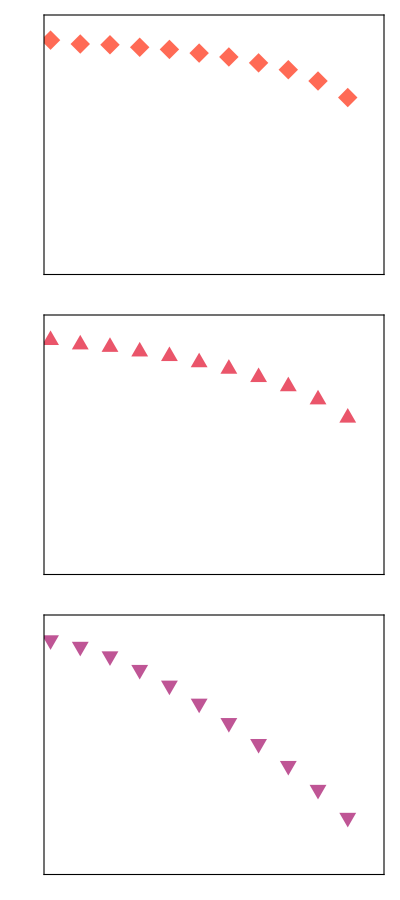

```mathematica
spcPlots//Transpose//Grid
```

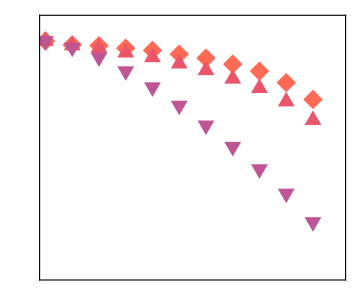

```mathematica
fs=22;
SetOptions[MaTeX,Magnification->1.4s];
pltjoint=Legended[Show[spcPlots[[1]]],
Placed[PointLegend[Reverse[{Lighter[Blend[{Orange,Red},0.75]],Lighter[Blend[{Red,Purple},0.25]],Lighter[Blend[{Red,Purple},0.75]]}],
MaTeX@Reverse[{"J_\\perp / J_\\parallel = 0.02","J_\\perp / J_\\parallel = 0.2","J_\\perp / J_\\parallel = 2"}],
LegendMarkerSize->16,Spacings->0.0,
LegendMarkers->Reverse[{{"◆",12s},{"▲",12s},{"▼",12s}}]],
{0.35,0.25}]
]
```

```mathematica
(*For[k=1,k<=Length[filelist],k++,(
Export["./plots/"<>filelist[[k]]<>".png",spcPlots[[k,1]],ImageResolution->300]
)]*)
Export["./plots/"<>"cn_2"<>".png",pltjoint,ImageResolution->300]
```

./plots/cn_2.png